## Canal One-Way Valve Model

No one-way valve, patent central canal

```mathematica
Quit
```

```mathematica
direction = 1;(* direction of the diod 0: normal, 1: reverse *)
dx = 10;  (* efficiency of the diode *)
diod[v_, r_, x_] := Which[
direction ==0,If[v>0, v/r,v/(x*r)],
direction==1, If[v<0,v/r, v/(x*r)]];
n=100;
cycle=1;(* cycle per sec of CSF wave *)
subaraP=13332.2;
pulseAmp=subaraP/5
en[t_]=pulseAmp* Sin[2 Pi*cycle* t/tperiod]+subaraP;
rc=1.78 10^11*100/n; (* central canal resistance *)
{{rs=6872*100/n;(* subarachnoid resistance *)}, {□}}
rpattern=1;
r=Which[
rpattern==1,Table[rc,n],
rpattern==2,Join[Table[rc,n/2-1],{100rc},Table[rc,n/2]],(* increased central canal resistance at point n/2 *)
rpattern==3,Join[Table[rc,n-1],{1000rc}](* increased central canal resistance at the filum terminale *)
];
Rpattern = 2;
R=Which[
Rpattern== 1,Table[rs,n],
Rpattern==2, Join[Table[rs,n/2-1],{100rs},Table[rs,n/2]](* increased subarachnoid resistance at point n/2 *)
];
Rflux=rc;
R0=rs;
Rout=rc;
dsub=10^(-4);
dtheca=100*10;
dcanal=10^(-9);
c=Table[dcanal,n-1];(* canal capacitance *)
d=Join[Table[dsub,n-1], {dtheca}];(* subarachnoid capacitance *)
Dcist=.1dsub;
k=25; (* location of one-way valve of the canal *)
Vob[t_]:=(Rout r[[1]] en[t] +Rflux r[[1]] Vcist[t]+Rflux Rout(v[1][t]+u[1][t]))/(Rout r[[1]]+Rflux r[[1]]+Rflux Rout);
eqn=Join[{v[1]'[t]==((Vob[t]-v[1][t]-u[1][t])/r[[1]]+(v[2][t]+u[2][t]-v[1][t]-u[1][t])/r[[2]])/c[[1]],
		u[1]'[t]==((Vcist[t]-u[1][t])/R[[1]]+(u[2][t]-u[1][t])/R[[2]]+c[[1]] v[1]'[t])/d[[1]],
		Vcist'[t]==((en[t]-Vcist[t])/R0+(Vob[t]-Vcist[t])/Rout+(u[1][t]-Vcist[t])/R[[1]])/Dcist},
	
Table[v[i]'[t]==((v[i-1][t]+u[i-1][t]-v[i][t]-u[i][t])/r[[i]]+(v[i+1][t]+u[i+1][t]-v[i][t]-u[i][t])/r[[i+1]])/c[[i]],{i,2,n-2}],
       Table[u[i]'[t]==((u[i-1][t]-u[i][t])/R[[i]]+(u[i+1][t]-u[i][t])/R[[i+1]]+c[[i]] v[i]'[t])/d[[i]],{i,2,n-1}],
		{v[n-1]'[t]==((v[n-2][t]+u[n-2][t]-v[n-1][t]-u[n-1][t])/r[[n-1]]+(u[n][t]-v[n-1][t]-u[n-1][t])/r[[n]])/c[[n-1]],
			u[n]'[t]==((v[n-1][t]+u[n-1][t]-u[n][t])/r[[n]]+(u[n-1][t]-u[n][t])/R[[n]])/d[[n]]},
		{Vcist[0]==100},
		Table[v[i][0]==0,{i,1,n-1}],
		Table[u[i][0]==subaraP,{i,1,n}]
			];
tperiod=5000;
analPeriod=20 tperiod;
funcs=Join[{Vcist},Table[v[i],{i,1,n-1}],Table[u[i],{i,1,n}]];
sol=NDSolve[eqn,funcs,{t,0,analPeriod},MaxSteps->3000000];
DuralTension[i_][t_]:=First[u[i][t]/.sol];
SyrinxTension[i_][t_]:=First[v[i][t]/.sol];
SubarachnoidFlow[i_][t_]:=First[(u[i][t]-u[i+1][t])/R[[i]]/.sol];
SyrinxFlow[i_][t_]:=First[(v[i][t]+u[i][t]-v[i+1][t]-u[i+1][t])/r[[i]]/.sol];
CanalFlow[i_][t_] :=  Which[
i ==1,First[ (Vob[t]-u[1][t]-v[1][t])/r[[1]]/.sol],
i==n,First[(u[n-1][t]+v[n-1][t]-u[n][t])/r[[n]]/.sol],
True,First[(u[i-1][t]+v[i-1][t]-u[i][t]-v[i][t])/r[[i]]/.sol]
]
```

2666.44

{{Null},{□}}

```mathematica
canalWave=Animate[ListLinePlot[
{
Table[{i,100DuralTension[i][t]/13332.2},{i,1,n-1}],       (* Dural Tension *)
Table[{i,0.2SyrinxTension[i][t]},{i,1,n-1}],       (*syrinx tension*)
Table[{i,1000SubarachnoidFlow[i][t]},{i,1,n-1}],   (*subarachnoid flow*)
Table[{i,100000000000CanalFlow[i][t]},{i,1,n}]   (* Central Canal Flow *)
},  
range1 = 200;
PlotRange->{-range1,range1},PlotLegends->{"Dural Tension","Syrinx Tenxion","Subarachnoid Flow","CanalFlow"}],{t,0,analPeriod},AnimationRate->tperiod]
```

```mathematica
simpleBlockWaves=Table[ListLinePlot[
{
Table[{i,100DuralTension[i][t]/13332.2},{i,1,n-1}],       (* Dural Tension *)
Table[{i,0.2SyrinxTension[i][t]},{i,1,n-1}],       (*syrinx tension*)
Table[{i,1000SubarachnoidFlow[i][t]},{i,1,n-1}],   (*subarachnoid flow*)
Table[{i,100000000000CanalFlow[i][t]},{i,1,n}]   (* Central Canal Flow *)
},  
range1 = 200;
PlotRange->{-range1,range1},PlotLegends->{"Dural Tension","Syrinx Tenxion","Subarachnoid Flow","CanalFlow"}],{t,10tperiod,15tperiod,100}];
```

```mathematica
Export["/home/chang/Dropbox/Projects/MRI_flow/mathematica/new_analysis/simpleBlockWaves.mp4",simpleBlockWaves]
```

/home/chang/Dropbox/Projects/MRI_flow/mathematica/new_analysis/simpleBlockWaves.mp4

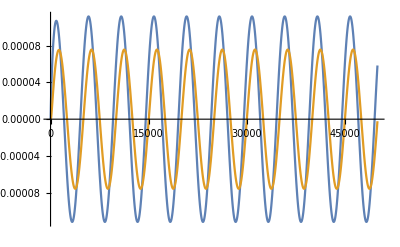

```mathematica
subaraWaveforms = Plot[{SubarachnoidFlow[5][t],SubarachnoidFlow[20][t]}, {t, 0, 10*5000}]
```

```mathematica
Export["/home/chang/Dropbox/Projects/MRI_flow/mathematica/concrete/subaraWaveforms.png",subaraWaveforms,ImageResolution->300]
```

/home/chang/Dropbox/Projects/MRI_flow/mathematica/concrete/subaraWaveforms.png

```mathematica
waveData=Table[{SubarachnoidFlow[5][t], SubarachnoidFlow[15][t]},{t, 0, 10*5000}]
```

{{0.,0.},{1.76748×10^-10,0.},{5.22387×10^-9,3.1019×10^-18},{2.87074×10^-8,1.1415×10^-15},{8.30288×10^-8,3.99174×10^-14},{1.73712×10^-7,4.40507×10^-13},{3.00475×10^-7,2.82682×10^-12},49987,{0.0000575915,0.0000136609},{0.0000577116,0.0000137653},{0.0000578315,0.0000138697},{0.0000579514,0.0000139741},{0.0000580712,0.0000140784},{0.0000581909,0.0000141828},{0.0000583105,0.0000142871}}
 |  |  |  |

```mathematica
Export["/home/chang/Dropbox/Projects/MRI_flow/mathematica/concrete/subaraWaveData.csv",waveData]
```

/home/chang/Dropbox/Projects/MRI_flow/mathematica/concrete/subaraWaveData.csv

```mathematica
myImages=Table[ListLinePlot[
{
Table[{i,DuralTension[i][t]},{i,1,n-1}],       (* Dural Tension *)
Table[{i,50SyrinxTension[i][t]},{i,1,n-1}],       (*syrinx tension*)
Table[{i,100000SubarachnoidFlow[i][t]},{i,1,n-1}],   (*subarachnoid flow*)
Table[{i,10000000000000CanalFlow[i][t]},{i,1,n}]   (* Central Canal Flow *)
},  
range1 = 200;
PlotRange->{-range1,range1},PlotLegends->{"Dural Tension","Syrinx Tenxion","Subarachnoid Flow","CanalFlow"}], {t,0,analPeriod,500}];
```

```mathematica
Export["mygif.gif",myImages]
```

mygif.gif